# Section 3.5 Derive

## Deriving Formulas in Mathematica

## Deriving Formulas in Mathematica

```mathematica
Clear["Global`*"]
```

One of the most powerful features in Mathematica is the ability to derive extremely complicated formulas simply and easily using basic theory.   However, it seems that this incredibly useful feature must be delayed until a Mathematica user has gained sufficient familiarity with the Mathematica syntax so as not to get lost.  Several preliminary observations are required before this process becomes easy.  Specifically, a Mathematica user must make the transition from "hand derivations" to Mathematica derivations.

Usually, "hand derivations" involve writing equations, substitutions and algebraic simplifications.  

On paper, a formula is entered as:
	lhs = rhs
However, in Mathematica equations are entered as:
	lhs == rhs
because "=" means assignment, not equality which is entered as "==".   Remember, equality is a "logical" operation, and not an "assignment" operation.

Substitution is achieved either by:
	 Assignment:
	 	lhs == rhs
	 	...
	 	a = value
	 	f[x_] := something
	 	...
	 	newEquation   =    lhs[...,a,...,f[x],...] == rhs[...,a,...,f[x],...]
	 	...
	 (Now newEquation contains:   lhs[...,value,...,something,...] == rhs[...,value,...,something,...])

	 Replacement rules:
	 	...
	 	newEquation   =    lhs[...,a,...] == rhs[...,a,...]   /.  a → value
	 	newEquation   =    lhs[...,f[x],...] == rhs[...,f[x],...]   /.  f[x] → something     (note the "x" and not "x_")
	 	...
	 (Now newEquation contains:   lhs[...,value,...,something,...] == rhs[...,value,...,something,...])
	 (Remember, you must re-assign the result so that it can be used later.)
	 
Algebraic simplification can be achieved by:
	lhs == rhs  // Simplify
	lhs == rhs  // FullSimplify
	
However, you need to realize the following points about the use of "==" related to simplification.
First, the head of "==" is "Equal" and that it is a logical operator:

```mathematica
FullForm[a==b]
```

Second, that the properties of  "==" do not automatically allow cancellation and simplification between the lhs and rhs.
For example, consider the following two cases:

```mathematica
3 + lhs==3+rhs
```

```mathematica
3 + lhs==3+rhs   // Simplify
```

Therefore, it is usually desirable to move all of the equation to just one side, so that simplification and cancellation can be performed:
	lhs  -  rhs  ==  0

```mathematica
(3 + lhs)- (3+rhs)  ==  0
```

Remark:  Moving all of the equation to just one side will not be necessary if your subsequent Mathematica commands directly manipulate the full equation (i.e. for example:   Solve, DSolve, NDSolve etc.).

Third, you will often want to operate on both sides of the equation (i.e. multiply, divide, differentiate, integrate etc.).  However, the Equal command does not automatically thread over other Mathematica commands.  
This is illustrated by the following examples:

```mathematica
3*(lhs == rhs)
```

```mathematica
(lhs1 == rhs1)  +  (lhs2 == rhs2)
```

```mathematica
(lhs1 == rhs1)  *  (lhs2 == rhs2)
```

```mathematica
∫(f[x] ==  x^2  +  1)ⅆx
```

Therefore, you must explicitly tell Mathematica to do this.  
Before showing you how to do this, consider the FullForm of the starting Mathematica expression:

```mathematica
3*(lhs == rhs)   //FullForm
```

Note that the "Times" command is on the outside and the "Equal" command is on the inside.  
Next, consider the FullForm of the expression that you want:

```mathematica
3*lhs==3*rhs   //FullForm
```

Note that the "Equal" command is on the outside and the "Times" command is on the inside.  
It is clear that you want to distribute (i.e. thread) the "Times[3, ... ]" over the  "Equal[lhs,rhs]".
This can be accomplished by using the Thread command:
	 Thread[  lhs == rhs,  Equal ]       (Remember, "Equal" is the head of "==")

```mathematica
Thread[  3*(lhs == rhs),  Equal ]
```

Consider the other examples:

```mathematica
Thread[ (lhs1 == rhs1)  +  (lhs2 == rhs2),  Equal ]
```

```mathematica
Thread[  (lhs1 == rhs1)  *  (lhs2 == rhs2),  Equal ]
```

```mathematica
Thread[ ∫(f[x]==1+x^2)ⅆx,  Equal ]
```

Using the above observations will usually let you derive even the most demanding formulas.

Finally, if your work demands repeated use of threading over the Equal command, then it may be convenient to define your own function which will accomplish this task automatically:

```mathematica
threadEqual[equation_] := Thread[ equation,  Equal ]
```

```mathematica
∫(f[x]==1+x^2)ⅆx //threadEqual
```

## Example: Derivation of the Single Pendulum Formula

Consider the simple mechanical problem of one pendulum attached to the ceiling.  We would like to derive the equations of motion for this problem.  See Figure 1.3 on page 7 of the book for the diagram.

-Graphics-

Although we could derive this problem directly by making specific algebraic substitutions and manipulations, we will instead derive this equation from more fundamental principles.  This will better illustrate the general procedure that one would use to derive formulas in Mathematica. (For our first example, we will manipulate the coordinate equations separately in our vector problem.)

Consider a pendulum consisting of a mass m1 and a rigid rod of length L1 for which: viscous damping, gravity and the forces applied through the rod are the primary forces acting upon the system.  Further, assume that the viscous forces are negatively proportional to the velocity of the pendulum mass.  Therefore, the vector form of Newton's law yields:
	m a⃗ = ∑ OverVector[F_i] =  OverVector[damping]  +  OverVector[gravity]  +  OverVector[rod forces]
	m a⃗ = ∑ OverVector[F_i] =   - k1 v⃗      -    m g⃗     -      OverVector[F_rod]
Expressing both the x and y components of the vector equation in Mathematica yields:
	m (x1''[t]
y1''[t]) == - k1 (x1'[t]
y1'[t]) - m (0
g) - F_rod (  Sin[θ1[t]]
-Cos[θ1[t]])
Separating the vector equation into its coordinate equations yields:
	m1*x1''[t] == - k1*x1'[t] - F_rod Sin[θ1[t]]
	m1*y1''[t] == - k1*y1'[t] +  m1*g + F_rod Cos[θ1[t]]
where F_rod is the scalar magnitude of the rod forces.

```mathematica
Clear["Global`*"]
```

```mathematica
m1 x1''[t]==-k1 x1'[t]-Subscript[F, rod] Sin[θ1[t]];

m1 y1''[t]==-k1 y1'[t]-m1 g+Subscript[F, rod] Cos[θ1[t]];
```

Our first step is to move the rhs to the lhs so that "all" of the equation is on just one side:

```mathematica
eq1x:=m1 x1''[t]+k1 x1'[t]+Subscript[F, rod] Sin[θ1[t]]==0;

eq1y:=m1 y1''[t]+k1 y1'[t]+m1 g-Subscript[F, rod] Cos[θ1[t]]==0;
```

The above equations represent free body motion.  However, we wish to impose the assumption that the pendulum rod is rigid, and therefore the pendulum mass can only move along the following coordinates. (Note that the angle θ1 is measured counterclockwise from the vertical downward position.  Therefore, the angle measured counterclockwise from the positive x-axis is given by θ1[t]+(3π)/2:

```mathematica
x1[t_]:=L1*Cos[θ1[t]+(3π)/2] ;

y1[t_]:=L1*Sin[θ1[t]+(3π)/2] ;
```

Notice that evaluation of the following two cells causes Mathematica to substitute for both x[t] and y[t], and to also evaluate the derivatives:

```mathematica
eq1x=Map[Simplify,eq1x]
```

```mathematica
eq1y=Map[Simplify,eq1y]
```

We could use a simple Mathematica command to combine the above equations in such a way as to eliminate the unknown value of F_rod.  However, we would like to illustrate how direct algebraic manipulations can be used to simplify the above equations (which is to multiply the first equation by Cos and the second equation by Sin, and then add the resulting equations):

```mathematica
eq1x = Thread[Cos[θ1[t]]*eq1x, Equal]
```

```mathematica
eq1y = Thread[Sin[θ1[t]]*eq1y, Equal]
```

```mathematica
finalEq = Thread[eq1x  +  eq1y, Equal]//Simplify
```

Observe that the above equation is exactly the same as Equation 1.9 on page 7 of the book.  Even though the derivation of this equation is not very complicated, it illustrates the fundamental steps that are used for the general derivation process.  
As a final remark, it is also possible to change the final appearance of the equation by removing the:  [t]   from the final expression.

```mathematica
finalEq/. head_[t]->head
```

Or change the symbolic notation even further:

```mathematica
finalEq/. head_[t]->head /.{θ1'->θ̇,θ1''->θ̈}
```

Remember, the above equation is not in standard Mathematica notation, and therefore can not be directly evaluated in its current form.

## Example: Derivation of the Double Pendulum Formulas

We can extend the above procedure to derive the equations of motion for a double pendulum system.  The upper pendulum will be designated as: 1, and the lower pendulum will be designated as: 2.

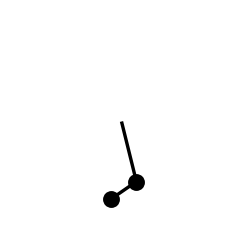

The first step is to use Newton's law on both pendulums.
Therefore, the vector form of Newton's law for the upper pendulum mass yields:
	m1 OverVector[a1] = ∑ OverVector[F1_i] =  OverVector[damping]  +  OverVector[gravity]  +  OverVector[rod forces]
	m1 OverVector[a1] = ∑ OverVector[F1_i] =  - k1 OverVector[v1]     -   m1 g⃗    +  (- OverVector[F_rod1]+OverVector[F_rod2])
where the rod force OverVector[F_rod1] on mass m1 is expressed in terms of its scalar magnitude F_rod1 and a vector of unit length pointing in the outward direction of the upper rod (which is expressed in terms of the angle θ1[t]).  The rod force on mass m1 produced by the lower rod OverVector[F_rod2] is likewise expressed in terms of a unit vector pointing outward in the direction of the lower rod at angle θ2[t].
	m1 (x1''[t]
y1''[t]) == - k1 (x1'[t]
y1'[t]) - m1 (0
g) - F_rod1 (  Sin[θ1[t]]
-Cos[θ1[t]]) + F_rod2 (  Sin[θ2[t]]
-Cos[θ2[t]])
The equation of motion for the lower rod is given by:
	m2 (x2''[t]
y2''[t]) == - k2 (x2'[t]
y2'[t]) - m2 (0
g) - F_rod2 (  Sin[θ2[t]]
-Cos[θ2[t]])
We will derive the above equations using Mathematica:

```mathematica
Clear["Global`*"]
```

First, define two vectors in rectangular coordinates as a function of time corresponding to the respective locations of masses m1 and m2:

```mathematica
Subscript[X, 1][t_]:=  {x1[t],y1[t]};
Subscript[X, 2][t_]:=  {x2[t],y2[t]};
```

For example, the vector acceleration of the first mass would be expressed as:

```mathematica
Subscript[X, 1]''[t]//MatrixForm
```

Define a vector formula which will calculate the direction of a unit vector pointing in the outward direction with angle θ.  Remember, our angle θ is to be measured counterclockwise from the vertical downward position, and therefore the correct representation for this angle measured counterclockwise from the positive x-axis is: θ + 3π/2.  We can use this formula for both the upper and lower rods by substituting either θ1 or θ2.

```mathematica
Subscript[uV, rod][θ_]:=  {Cos[θ+(3π)/2],Sin[θ+(3π)/2]}
```

For example, the outward unit vector for the upper rod at time t would be:

```mathematica
Subscript[uV, rod][θ1[t]]//MatrixForm
```

The vector equation of motion for the upper rod becomes:

```mathematica
vectorEqs1 = 

m1*Subscript[X, 1]''[t]==- k1*Subscript[X, 1]'[t] +m1*{0,-g}-Subscript[F, rod1]*Subscript[uV, rod][θ1[t]]+Subscript[F, rod2]*Subscript[uV, rod][θ2[t]]
```

The vector equation of motion for the lower rod becomes:

```mathematica
vectorEqs2 = 

m2*Subscript[X, 2]''[t]==- k2*Subscript[X, 2]'[t] +m2*{0,-g}-Subscript[F, rod2]*Subscript[uV, rod][θ2[t]]
```

Observe that we need to Thread "==" over the List (because vectors are represented as 1-dimensional lists).  Therefore, the vector equation for the upper pendulum becomes:

```mathematica
vectorEqs1  =   Thread[ vectorEqs1 ,List]
```

The vector equation for the lower pendulum becomes:

```mathematica
vectorEqs2  =   Thread[ vectorEqs2 ,List]
```

Display all 4 equations of motion:

```mathematica
vectorEqs1∪vectorEqs2// TableForm
```

The above equations represent free body motion.  However, we wish to impose the assumption that both pendulum rods are rigid, and therefore each pendulum mass can only move with the following coordinates. (Note that the angles θ1 and θ2 are measured counterclockwise from the vertical downward position.  Therefore, the angles measured counterclockwise from the positive x-axis are given by θ1[t]+(3π)/2 and θ2[t]+(3π)/2.

```mathematica
x1[t_]:=L1*Cos[θ1[t]+(3π)/2] ;

y1[t_]:=L1*Sin[θ1[t]+(3π)/2] ;

x2[t_]:=L1*Cos[θ1[t]+(3π)/2] + L2*Cos[θ2[t]+(3π)/2];

y2[t_]:=L1*Sin[θ1[t]+(3π)/2] + L2*Sin[θ2[t]+(3π)/2];
```

Notice that evaluation of the above 4 ODE formulas causes Mathematica to substitute for: x1[t], y1[t], x2[t], y2[t] and to also evaluate the derivatives:

```mathematica
allEqns=vectorEqs1∪vectorEqs2
```

Display all four equations:

```mathematica
allEqns//TableForm
```

Examination of the above 4 formulas indicates that we need to eliminate the two unknown scalar magnitudes: F_rod1and F_rod2.   This can be accomplished directly by using the Eliminate command.  However the Eliminate command can make a number of different choices on how to eliminate 2 variables from 4 equations.  Therefore, the Eliminate command returns a number of acceptable formulas from which the 2 variables have been removed.  It expects that you will select the formulas that you like best from the offering.  The returned formulas are connected by "And" because they are not necessarily independent of each other (i.e. the returned formulas are given as:    lhs1==rhs1 && lhs2==rhs2 && lhs3==rhs3 &&  ...).  
Therefore, it will be easier in our case to select 3 formulas and eliminate both F_rod1and F_rod2 producing a single resulting formula.  We will do this twice to obtain 2 independent formulas.   Start by using both of the upper pendulum coordinate equations and only the first (i.e. x-coordinate) lower pendulum equation:

```mathematica
firstEqn = 

Eliminate[

vectorEqs1∪{vectorEqs2⟦1⟧},

{Subscript[F, rod1],Subscript[F, rod2]}
]
```

Simplify the result:

```mathematica
firstEqn = firstEqn//Simplify
```

Next use both of the upper pendulum coordinate equations and only the second (i.e. y-coordinate) lower pendulum equation:

```mathematica
secondEqn = 

Eliminate[

vectorEqs1∪{vectorEqs2⟦2⟧},

{Subscript[F, rod1],Subscript[F, rod2]}
]
```

Simplify the result:

```mathematica
secondEqn = secondEqn//Simplify
```

The above 2 nonlinear second-order coupled ODEs represent the motion of our double pendulum system.

## Numerical Solutions for the Double Pendulum Problem

The formulas for the double pendulum problem are both nonlinear and second order.  A symbolic solution to our nonlinear problem is not expected.  Therefore, only numerical examples will be generated.  Consider some reasonable values for the lengths, masses and friction coefficients for each of the two pendulums:

```mathematica
L1=2;
m1=1;
k1=.5;
L2=1;
m2=1;
k2=k1;
g=32;
```

Observe the form of our second-order nonlinear ODE equations after substituting the above values:

```mathematica
firstEqn
```

```mathematica
secondEqn
```

Numerically solve the ODE system using an initial angular displacement and initial angular velocity for each of the two pendulums.  (Note that I chose to express the ODE equations in terms of θ1 and θ2, which are also used in the above formulas.  Therefore, it is extremely important that both θ1 and θ2 are cleared before calling NDSolve.)
Basically, the initial conditions correspond to moving the lower pendulum counterclockwise 1.5 radians and letting go with zero angular velocity.

```mathematica
Clear[θ1,θ2];

solnRules=

NDSolve[

{
firstEqn,
secondEqn,
θ1[0]==0,
θ1'[0]==0,
θ2[0]==1.5,
θ2'[0]==0
},

{θ1,θ2},

{t,0,10}
]
```

Extract the two angle solutions.  (Note that I must use θ1 and θ2 as the names of my solutions if I want to use the formulas for x1[t] and x2[t] defined above.  One consequence of this action is that I must clear both θ1 and θ2 before re-calling NDSolve.)

```mathematica
θ1 = θ1/.Flatten[solnRules]
```

```mathematica
θ2 = θ2/.Flatten[solnRules]
```

Plot the two angular displacements as a function of time:

```mathematica
Plot[

{θ1[t],θ2[t]},

{t,0,10},

PlotStyle->{{Thickness[.007],Dashing[{}]},{Thickness[.007],Dashing[{.01,.01}]}},
PlotRange->All,
ImageSize->6 72,
AspectRatio->.5
]
```

## Animate the Double Pendulum Solution

Generate a module which will use graphic primitives to display the positions of the two pendulums:

```mathematica
plotPendulums[t_]:=

Module[

{totalL=1.07 (L1+L2)},

Show[
Graphics[

{Thickness[.01],
Line[{{0,0},{x1[t],y1[t]}}],

PointSize[(.1 m1)/(m1+m2)],
Point[{x1[t],y1[t]}],

Line[{{x1[t],y1[t]},{x2[t],y2[t]}}],

PointSize[(.1 m2)/(m1+m2)],
Point[{x2[t],y2[t]}]}
],

AspectRatio->1,
Axes->Automatic,
Ticks->None,
AxesStyle->GrayLevel[.5],
PlotRange->{{-totalL,totalL},{-totalL,totalL}}
]
]
```

The initial pendulum displacements are at t=0:

```mathematica
plotPendulums[0]
```

Generate a time animation of plots to indicate the pendulum positions as a function of time:

```mathematica
Animate[

plotPendulums[t],

{t,0,10},

DefaultDuration->10

]
```

Animate the above plot, while slowing the animation using the controls located at the top.  Observe that the motion of the lower pendulum causes the upper pendulum to move as well.  Eventually, the viscous damping will slow the pendulums until they stop moving,

## Additional Animations

Consider an example where the initial displacements for our two pendulums is much greater, which better illustrates the nonlinear nature of our solution:

```mathematica
L1=2;
m1=2;
k1=.5;
L2=1;
m2=1;
k2=k1;
g=32;
maxTime=15;
```

Solve the nonlinear ODE system for these values:

```mathematica
Clear[θ1,θ2];

solnRules=

NDSolve[

{
firstEqn,
secondEqn,
θ1[0]==2,
θ1'[0]==0,
θ2[0]==3,
θ2'[0]==0
},

{θ1,θ2},

{t,0,maxTime},

MaxSteps->5000
]
```

Extract the two angle solutions:

```mathematica
θ1 = θ1/.Flatten[solnRules]
```

```mathematica
θ2 = θ2/.Flatten[solnRules]
```

Plot the two angular displacements as a function of time:

```mathematica
Plot[

{θ1[t],θ2[t]},

{t,0,maxTime},

PlotStyle->{{Thickness[.007],Dashing[{}]},{Thickness[.007],Dashing[{.01,.01}]}},
PlotRange->All,
ImageSize->6 72
]
```

The initial pendulum angular displacements are:

```mathematica
plotPendulums[0]
```

Animate a time sequence of plots to indicate the pendulum positions as a function of time:

```mathematica
Animate[

plotPendulums[t],

{t,0,maxTime},

DefaultDuration->maxTime
]
```

Animate the plots, while slowing the animation using the controls located at the top.  Observe that the motion of the lower pendulum causes the upper pendulum to move as well.  Eventually, the viscous damping will slow the pendulums until they stop moving,

## Visualizing the Four-Dimensional Phase Space

The following development is intended to illustrate how the behavior of each individual pendulum is interrelated by the coupled nonlinear second-order ODE system.  What we would like to do, is examine the phase plane for each individual pendulum.  However, the phase plane of one pendulum depends directly upon the current behavior of the other pendulum, and therefore is not constant in time.  The correct way to visualize this problem is as a four-dimensional phase space, rather than two separate phase planes.  The solution orbits would move in this four-dimensional phase space producing the range of behavior illustrated above.  However, there is no way to display a four-dimensional graph on a computer screen.  Therefore, we will illustrate some of the behavior of the four-dimensional phase space by graphing two 2-dimensional slices.  One 2-dimensional slice corresponds to θ1 and θ1' for fixed values of both θ2 and θ2'.  The second 2-dimensional slice corresponds to θ2 and θ2' for fixed values of both θ1 and θ1'.  Please understand that the 2-dimensional slices move through the four-dimensional phase space in such a way as to follow the solution orbit.  Therefore, as expected, each 2-dimensional phase plane will exhibit behavior related to the behavior of the other, and will therefore change with time.  However, please realize that the overall behavior of the 4-dimensional phase space is time independent because the coefficients in the second order nonlinear ODE system are all independent of time.  Therefore, a solution orbit starting with initial conditions θ1, θ1', θ2 and θ2' will follow a unique path through the 4-dimensional phase space.

Our first step is to reduce the two second-order ODEs into four first-order ODEs.  This is accomplished in the usual way by introducing new variables:
	θ1[t]→θ1a
	θ1'[t]→θ1p
	θ2[t]→θ2a
	θ2'[t]→θ2p

```mathematica
Clear[L1,m1,k1,L2,m2,k2,g,θ1,θ2]
```

```mathematica
rules=

{θ1[t]->θ1a,
θ1'[t]->θ1p,
θ2[t]->θ2a,
θ2'[t]->θ2p};
```

Recall that our two second-order ODEs are contained in: firstEqn and secondEqn.  Also, reducing a second order ordinary differential equation to a first-order system will introduce two additional ODEs (which arise from the definition of our new variables):
	θ1'[t] = θ1p
	θ2'[t] = θ2p
Create a list of all four first-order differential equations and substitute the new variables into the right hand side of each equation:

```mathematica
allEqs=

{
θ1'[t]==θ1p,

firstEqn/.rules,

θ2'[t]==θ2p,

secondEqn/.rules
}
```

Rearrange our first order system of four equations so that the terms containing the first-order derivatives appear on the left-hand side (Observe that I did not explicitly express the second derivatives as first derivatives in the new variables, i.e. θ1''[t] = θ1p' and θ2''[t] = θ2p'):

```mathematica
allEqsNew=

Simplify[

Solve[

allEqs,

{θ1'[t],θ1''[t],θ2'[t],θ2''[t]}
]
]
```

Examine our replacement rules in TableForm:

```mathematica
allEqsNew//Flatten//TableForm
```

Define our first 2-dimensional slice of the four-dimensional phase plane:

	{θ1a,θ1p,θ2a,θ2p} = {θ1a,θ1p,θ2'[t],θ2''[t]}
	
where the 2 dimensional slice passes through the point {θ2'[t],θ2''[t]} containing the current value of the solution orbit for the second pendulum.  Remember, θ1'[t] and θ1''[t] will be replaced by the right hand side of the ODE system calculated above:

```mathematica
f1[θ1a_,θ1p_,θ2a_,θ2p_]=

{θ1'[t],θ1''[t]} /.Flatten[allEqsNew]
```

Define our second 2-dimensional slice of the four-dimensional phase plane:
	{θ1a,θ1p,θ2a,θ2p} = {θ1'[t],θ1''[t],θ2a,θ2p}
where the 2 dimensional slice passes through the point {θ1'[t],θ1''[t]} containing the current value of the solution orbit for the first pendulum.  Remember, θ2'[t] and θ2''[t] will be replaced by the right hand side of the ODE system calculated above:

```mathematica
f2[θ1a_,θ1p_,θ2a_,θ2p_]=

{θ2'[t],θ2''[t]} /.Flatten[allEqsNew]
```

Specify the same numerical values for our system parameters as used in the previous section:

```mathematica
L1=2;
m1=2;
k1=.5;
L2=1;
m2=1;
k2=k1;
g=32;
maxTime=15;
```

Solve our ODE system:

```mathematica
Clear[θ1,θ2];

solnRules=

NDSolve[

{
firstEqn,
secondEqn,
θ1[0]==2,
θ1'[0]==0,
θ2[0]==3,
θ2'[0]==0
},

{θ1,θ2},

{t,0,maxTime},

MaxSteps->5000
]
```

Extract our two solutions:

```mathematica
θ1 = θ1/.Flatten[solnRules]
```

```mathematica
θ2 = θ2/.Flatten[solnRules]
```

The following graph illustrates the behavior of the first pendulum in terms of: θ1[t] and θ1'[t].  The behavior illustrated below is very involved, and would require a tremendous number of vector field graphs in order to visualize correctly.  Therefore, we are going to illustrate the changing 2-dimensional slice of the four-dimensional phase plane only over the time interval from 0 to 4.  This shorter time interval still contains significant behavior, but is short enough to allow an animation on your computer system.

```mathematica
Show[

Graphics[

{
Hue[.15],
Rectangle[{0,-6},{4,7}]
},

Axes->True
],

Plot[

{θ1[t],θ1'[t]},

{t,0,6},

PlotStyle->{{Thickness[.007],Dashing[{}]},{Thickness[.007],Dashing[{.01,.01}]}}

],
AspectRatio->.5,
ImageSize->6 72
]
```

The following graph illustrates the behavior of the second pendulum in terms of: θ2[t] and θ2'[t].   We are going to illustrate the changing 2-dimensional slice of the four-dimensional phase plane only over the time interval from 0 to 4.  This shorter time interval still contains significant behavior, as illustrated by the second pendulum "looping" over the "top" at the end of our time interval:

```mathematica
Show[

Graphics[

{
Hue[.15],
Rectangle[{0,-25},{4,22}]
},

Axes->True
],

Plot[

{θ2[t],θ2'[t]},

{t,0,6},

PlotStyle->{{Thickness[.007],Dashing[{}]},{Thickness[.007],Dashing[{.01,.01}]}}

],
AspectRatio->.7,
ImageSize->6 72
]
```

The following Mathematica functions will be used to generate a pair of 2-dimensional vector fields (one for the top pendulum and one for the bottom pendulum).  Also, the left vector field will have a schematic which illustrates the current configuration of both the top and bottom pendulums.
Define a function which will plot the 2-dimensional vector field "slice" for the top pendulum:

```mathematica
vecField1[t_]:=

VectorPlot[

f1[θ1a,θ1p,θ2[t],θ2'[t]],

{θ1a,-π,π},
{θ1p,-10,10},

AspectRatio->1,
Frame->True
]
```

Define a function which will plot the 2-dimensional vector field "slice" for the bottom pendulum:

```mathematica
vecField2[t_]:=

VectorPlot[

f2[θ1[t],θ1'[t],θ2a,θ2p],

{θ2a,-3,6},
{θ2p,-20,20},

AspectRatio->1,
Frame->True
]
```

Use a large red point to illustrate the current location of our solution orbit in the first "phase plane" slice.  Also, superimpose the position at time t of the dual pendulums in a smaller rectangular region located in the upper left-hand corner:

```mathematica
plot1[t_]:=

Show[

vecField1[t],

Graphics[
{
{RGBColor[1,0,0],PointSize[0.03],Point[{θ1[t],θ1'[t]}]},
Inset[plotPendulums[t],{-π/2,5.5},{0,0},4]
}
],
ImageSize->{72 4.5,72 4.5}
]
```

Use a large red point to illustrate the current location of our solution orbit in the second "phase plane" slice:

```mathematica
plot2[t_]:=

Show[

vecField2[t],

Graphics[
{RGBColor[1,0,0],PointSize[.03],Point[{θ2[t],θ2'[t]}]}
],
ImageSize->{72 4,72 4}
]
```

Show both 2-dimensional phase plane slices side by side (the top pendulum corresponds to the left vector field and the bottom pendulum corresponds to the right vector field):

```mathematica
plot12[t_]:=

Show[

GraphicsGrid[

{{plot1[t],plot2[t]}}

],
ImageSize->{72 8,72 4}
]
```

Generate the graphs for our animation (The time and computer memory requirements required to generate this sequence of plots may exceed the capability of your equipment.  If this occurs, try increasing the time step size from .02 to a larger number):

```mathematica
NotebookWrite[
EvaluationNotebook[],
Cell[
BoxData[
ToBoxes[
Animate[plot12[t],{t,0,4,.02},DisplayAllSteps->True]
]
],
ShowStringCharacters->False
]
]
```

Animate the above vector fields (the top pendulum corresponds to the left vector field and the bottom pendulum corresponds to the right vector field).  Remember to slow down the above animation significantly so that the changing vector fields can be better understood. This can be achieved by using the animation speed controls: ∧ and ∨ located at the top.  However, becuse the information in the above animation is changing so quickly, it may be desirable to step through the animation one frame at a time.  This can be accomplished by:
	 First, click the "pause" button "||" located at the top.
	 Second, drag the "slider" bar very slowly one frame at a time.  The relative location of the current frame being displayed within the full animation is indicated by the "slider" bar position.


Observe that the equilibrium point for the top pendulum shifts its location close to the solution orbit about midway through the animation.  Observe that this situation occurs when both the top and the bottom pendulums are pointing in the same direction.  Therefore, at this time the top pendulum momentarily "pauses" until the bottom pendulum changes its angle sufficiently to produce a non-canceling force on the top pendulum.
Also observe that the bottom pendulum eventually goes up and over the top 2/3 through the animation (and from that time on, the red dot corresponding to the angle θ2 exceeds 6 and goes off the vector field plot).  Remember, the positive direction of the angle θ2 is measured counterclockwise from the downward direction, and when the bottom pendulum goes over the top, then θ2 increases positively beyond π radians (i.e. it moves beyond π in the second phase plane).